# Plotting the colony cycle

The output from the Excel file is a table (on the Outputs tab). Copy it into the following command (between the “”) and click ‘Yes’:

```mathematica
data=ImportString[
"Month\t-1\t0\t1\t2\t3\t4\t5\t6\t7\t8\t9\t10\t11\t12\t13\t14
Total observations\t37\t29\t33\t26\t42\t74\t58\t21\t22\t13\t27\t43\t37\t29\t33\t26
Off-nest female\t15\t10\t18\t12\t14\t36\t29\t10\t10\t6\t14\t21\t15\t10\t18\t12
Nest (foundress, no large larvae)\t1\t0\t1\t3\t0\t3\t3\t1\t4\t2\t5\t0\t1\t0\t1\t3
Nest (foundress, large larvae without pupae)\t2\t0\t2\t1\t1\t0\t1\t0\t1\t0\t3\t2\t2\t0\t2\t1
Nest (foundress, containing pupae)\t5\t0\t0\t0\t0\t0\t1\t0\t0\t0\t0\t8\t5\t0\t0\t0
Nest (foundress)\t17\t9\t3\t4\t1\t3\t5\t1\t5\t3\t8\t13\t17\t9\t3\t4
Post-emergence nest\t3\t9\t6\t7\t12\t17\t7\t1\t1\t1\t3\t5\t3\t9\t6\t7
Lek\t0\t0\t0\t0\t0\t2\t0\t0\t0\t0\t0\t0\t0\t0\t0\t0
Hibernation cluster\t0\t0\t0\t0\t0\t1\t2\t2\t2\t1\t0\t0\t0\t0\t0\t0
Dead female\t1\t0\t2\t1\t1\t1\t1\t0\t1\t0\t1\t1\t1\t0\t2\t1
Dead male\t0\t0\t0\t0\t0\t0\t0\t0\t0\t0\t0\t0\t0\t0\t0\t0
Male (off nest)\t1\t1\t3\t2\t2\t10\t13\t3\t2\t1\t0\t0\t1\t1\t3\t2
","TSV"];
```

Check it worked by using TableForm to show the table:

```mathematica
TableForm[data]
```

Month | -1 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
Total observations | 37 | 29 | 33 | 26 | 42 | 74 | 58 | 21 | 22 | 13 | 27 | 43 | 37 | 29 | 33 | 26
Off-nest female | 15 | 10 | 18 | 12 | 14 | 36 | 29 | 10 | 10 | 6 | 14 | 21 | 15 | 10 | 18 | 12
Nest (foundress, no large larvae) | 1 | 0 | 1 | 3 | 0 | 3 | 3 | 1 | 4 | 2 | 5 | 0 | 1 | 0 | 1 | 3
Nest (foundress, large larvae without pupae) | 2 | 0 | 2 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 3 | 2 | 2 | 0 | 2 | 1
Nest (foundress, containing pupae) | 5 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 8 | 5 | 0 | 0 | 0
Nest (foundress) | 17 | 9 | 3 | 4 | 1 | 3 | 5 | 1 | 5 | 3 | 8 | 13 | 17 | 9 | 3 | 4
Post-emergence nest | 3 | 9 | 6 | 7 | 12 | 17 | 7 | 1 | 1 | 1 | 3 | 5 | 3 | 9 | 6 | 7
Lek | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Hibernation cluster | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 2 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0
Dead female | 1 | 0 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 2 | 1
Dead male | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Male (off nest) | 1 | 1 | 3 | 2 | 2 | 10 | 13 | 3 | 2 | 1 | 0 | 0 | 1 | 1 | 3 | 2

General parameters for plotting:

```mathematica
MyAspectRatio=1/10;
MyThickness=0.005;
PlotLineOpacity=0.3;
```

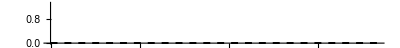

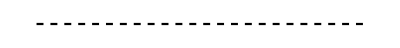

```mathematica
AllObservationsColour=Gray;
FoundressColour=Cyan;
PostEmergenceColour=Black;
OffNestFemaleColour=Gray;
OffNestMaleColour=Orange;
HibernationClusterColour=Gray;

EmptyPlot=Plot[0,{x,1,12},PlotStyle->{Black,Opacity[1],Dashed},Axes->{True,False},Ticks->{
{
{1,"J"},
{2,"F"},
{3,"M"},
{4,"A"},
{5,"M"},
{6,"J"},
{7,"J"},
{8,"A"},
{9,"S"},
{10,"O"},
{11,"N"},
{12,"D"}},Automatic},TicksStyle->Directive[Black,16],AspectRatio->MyAspectRatio,PlotRange->{{1,12},{0,1.3}}]

InvertedEmptyPlot=Plot[0,{x,1,12},PlotStyle->{Black,Opacity[1],Dashed},Axes->{False}
,AspectRatio->MyAspectRatio,PlotRange->{{1,12},{0,-1.3}}]
```

```mathematica
FoundressColour
```

RGBColor[0, 1, 1]

## (1) Plotting total observations:

```mathematica
MyRow=2;
```

Total observations are in row 2 (which is data[[2]]). 

Transpose the points, so that it is in a usable format. I will also scale each set of observations as a proportion of the highest value for that observation type:

```mathematica
pts=Transpose[{data[[1]],data[[MyRow]]/(Max[data[[MyRow]]][[1]])}] ;(*data[[1]] is the month. The second part is the variable we're interested in plotting.*)
pts=pts[[2;;16]] (*Removes the first bit, which is {"Month","Total observations"}*)
```

{{-1,1/2},{0,29/74},{1,33/74},{2,13/37},{3,21/37},{4,1},{5,29/37},{6,21/74},{7,11/37},{8,13/74},{9,27/74},{10,43/74},{11,1/2},{12,29/74},{13,33/74}}

To generate a smooth function, we will use the Interpolation function in Mathematica:

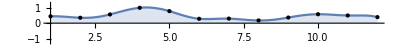

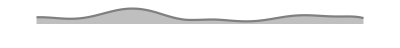

```mathematica
ifun=Interpolation[pts,InterpolationOrder->10];

Plot[ifun[x],{x,1,12},Epilog->Point[pts],Filling->Axis,AspectRatio->1/10,PlotRange->{{1,12},{-1.3,1.3}}]

(*That shows whether it works. We don't want to include the points, however, in the actual plot, which is exactly the same just without the Epilog part and the axes:*)

Plot1=Plot[ifun[x],{x,1,12},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],AllObservationsColour],
PlotStyle->AllObservationsColour,
AspectRatio->MyAspectRatio,
PlotRange->{{1,12},{-1.3,1.3}},Axes->{False}]
```

I would like to make this graph symmetrical around the origin, as a fun way of plotting the data:

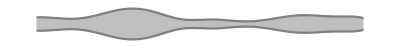

```mathematica
ifun=Interpolation[pts,InterpolationOrder->10];

Plot2=Plot[-ifun[x],{x,1,12},Epilog->Point[pts],
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],AllObservationsColour],
PlotStyle->AllObservationsColour,
AspectRatio->MyAspectRatio,
PlotRange->{{1,12},{-1.3,1.3}},Axes->{False}];

AllObservationsPlot=Show[Plot1,Plot2]
```

The following sections use the same method:

## (2) Plotting foundress nests:

```mathematica
MyRow=7;
```

Foundress nest (any stage) observations are in row 7 (which is data[[7]]). 

Transpose the points, so that it is in a usable format:

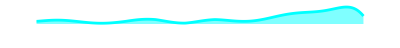

```mathematica
pts=Transpose[{data[[1]],data[[MyRow]]/(Max[data[[MyRow]]][[1]])}] ;
pts=pts[[2;;16]] ;
ifun=Interpolation[pts,InterpolationOrder->10];

Plot1=Plot[ifun[x],{x,1,12},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],FoundressColour],
PlotStyle->{FoundressColour,Thickness[MyThickness]},
AspectRatio->MyAspectRatio,
PlotRange->{{1,12},{-1.3,1.3}},Axes->{False}];

Plot2=Plot[-ifun[x],{x,1,12},Epilog->Point[pts],
Filling->Axis,
FillingStyle->Directive[Opacity[0.2],FoundressColour],
PlotStyle->{PlotLineOpacity,Thickness[MyThickness]},
AspectRatio->MyAspectRatio,
PlotRange->{{1,12},{-1.3,1.3}},Axes->{False}];

FoundressPlot=Show[Plot1]
```

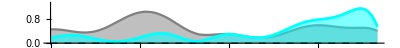

```mathematica
Show[EmptyPlot,AllObservationsPlot,FoundressPlot]
```

## (3) Plotting post-emergence nests:

```mathematica
MyRow=8;
```

Post-emergence nest observations are in row 8 (which is data[[8]]). 

Transpose the points, so that it is in a usable format:

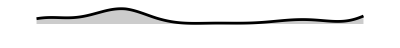

```mathematica
pts=Transpose[{data[[1]],data[[MyRow]]/(Max[data[[MyRow]]][[1]])}] ;
pts=pts[[2;;16]] ;
ifun=Interpolation[pts,InterpolationOrder->10];

Plot1=Plot[ifun[x],{x,1,12},
Filling->Axis,
FillingStyle->Directive[Opacity[0.2],PostEmergenceColour],
PlotStyle->{PostEmergenceColour,Thickness[MyThickness]},
AspectRatio->MyAspectRatio,
PlotRange->{{1,12},{-1.3,1.3}},Axes->{False}];

Plot2=Plot[-ifun[x],{x,1,12},Epilog->Point[pts],
Filling->Axis,
FillingStyle->Directive[Opacity[0.2],PostEmergenceColour],
PlotStyle->{PostEmergenceColour,Thickness[MyThickness]},
AspectRatio->MyAspectRatio,
PlotRange->{{1,12},{-1.3,1.3}},Axes->{False}];

PostEmergencePlot=Show[Plot1]
```

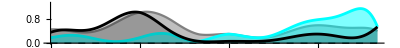

```mathematica
Show[EmptyPlot,AllObservationsPlot,FoundressPlot,PostEmergencePlot]
```

## (4) Plotting off-nest females:

Post-emergence nest observations are in row 3 (which is data[[3]]).

```mathematica
MyRow=3;
```

Transpose the points, so that it is in a usable format:

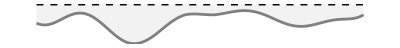

```mathematica
pts=Transpose[{data[[1]],data[[MyRow]]/(Max[data[[MyRow]]][[1]])}] ;
pts=pts[[2;;16]] ;
ifun=Interpolation[pts,InterpolationOrder->10];

Plot1=Plot[ifun[x],{x,1,12},
Filling->Axis,
FillingStyle->Directive[Opacity[0.4],OffNestFemaleColour],
PlotStyle->{OffNestFemaleColour,Thickness[MyThickness]},
AspectRatio->MyAspectRatio,
PlotRange->{{1,12},{-1.3,1.3}},Axes->{False}];

Plot2=Plot[-ifun[x],{x,1,12},Epilog->Point[pts],
Filling->Axis,
FillingStyle->Directive[Opacity[0.1],OffNestFemaleColour],
PlotStyle->{OffNestFemaleColour,Thickness[MyThickness]},
AspectRatio->MyAspectRatio,
PlotRange->{{1,12},{-1.3,1.3}},Axes->{False}];

OffNestFemalePlot=Show[InvertedEmptyPlot,Plot2]
```

## (5) Plotting off-nest males:

Off-nest male observations are in row 13 (which is data[[13]]).

```mathematica
MyRow=13;
```

Transpose the points, so that it is in a usable format:

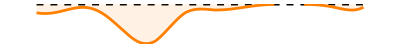

```mathematica
pts=Transpose[{data[[1]],data[[MyRow]]/(Max[data[[MyRow]]][[1]])}] ;
pts=pts[[2;;16]] ;
ifun=Interpolation[pts,InterpolationOrder->10];

Plot1=Plot[ifun[x],{x,1,12},
Filling->Axis,
FillingStyle->Directive[Opacity[0.2],OffNestMaleColour],
PlotStyle->{OffNestMaleColour,Thickness[MyThickness]},
AspectRatio->MyAspectRatio,
PlotRange->{{1,12},{0,1.3}},Axes->{False}];

Plot2=Plot[-ifun[x],{x,1,12},Epilog->Point[pts],
Filling->Axis,
FillingStyle->Directive[Opacity[0.1],OffNestMaleColour],
PlotStyle->{OffNestMaleColour,Thickness[MyThickness]},
AspectRatio->MyAspectRatio,
PlotRange->{{1,12},{-1.3,0}},Axes->{False}];

OffNestMalePlot=Show[InvertedEmptyPlot,Plot2]
```

## (6) Plotting hibernation clusters (this only applies in the south, of course):

Hibernation cluster observations are in row 10 (which is data[[10]]).

```mathematica
MyRow=10;
```

Transpose the points, so that it is in a usable format:

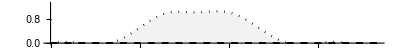

```mathematica
pts=Transpose[{data[[1]],data[[MyRow]]/(Max[data[[MyRow]]][[1]])}] ;
pts=pts[[2;;16]] ;
ifun=Interpolation[pts,InterpolationOrder->10];

Plot1=Plot[ifun[x],{x,1,12},
Filling->Axis,
FillingStyle->Directive[Opacity[0.1],HibernationClusterColour],
PlotStyle->{Black,Dotted},
AspectRatio->MyAspectRatio,
PlotRange->{{1,12},{0,1.3}},Axes->{False}];

Plot2=Plot[-ifun[x],{x,1,12},Epilog->Point[pts],
Filling->Axis,
FillingStyle->Directive[Opacity[0.2],HibernationClusterColour],
PlotStyle->{HibernationClusterColour,Dashed},
AspectRatio->MyAspectRatio,
PlotRange->{{1,12},{-1.3,0}},Axes->{False}];

HibernationClusterPlot=Show[EmptyPlot,Plot1]
```

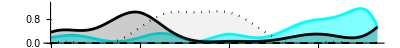

```mathematica
Show[EmptyPlot,FoundressPlot,PostEmergencePlot,HibernationClusterPlot]
```

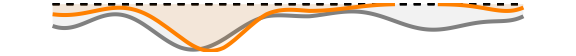

```mathematica
WaspsPlot=Show[InvertedEmptyPlot,OffNestFemalePlot,OffNestMalePlot,ImageSize->Large]
```

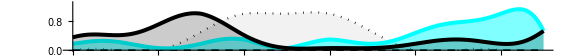

```mathematica
GroupsPlot=Show[EmptyPlot,HibernationClusterPlot,FoundressPlot,PostEmergencePlot,ImageSize->Large]
```

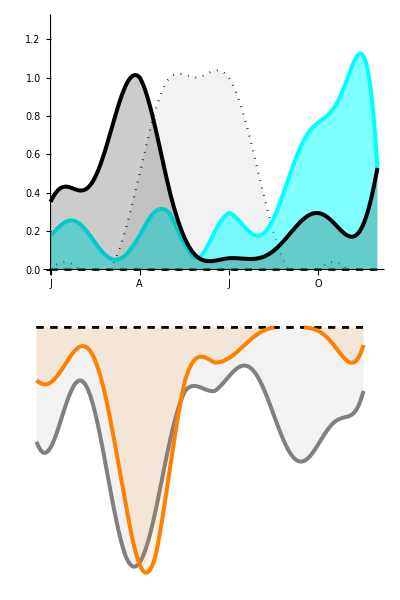

```mathematica
OutputGraph=Grid[{
{GroupsPlot},{WaspsPlot}
}]
```

```mathematica
Export["SeasonalTemperateAfrica.svg",OutputGraph]
```

SeasonalTemperateAfrica.svg

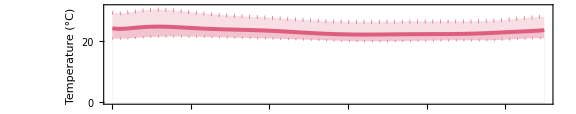
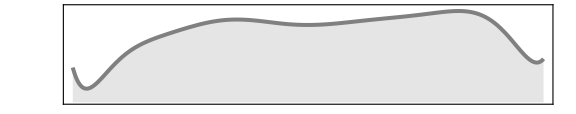
-Graphics-
-Graphics--Graphics-

```mathematica
Grid[{
{OutputGraph},{ClimateOutput}
}]
```